```mathematica
(* MHD + radiation coupled *)
(* linear wave in x, but solved on a plane with u1,u2,B1,B2.neq.0 *)
```

```mathematica
(* to zero 2nd order *)
s2nd={
δu1 δu1->0,
δu1 δu2->0,
δu1 δB1->0,
δu1 δB2->0,
δu1 δρ->0,
δu1 δu->0,
δu1 δEE->0,
δu1 δF1->0,
δu1 δF2->0,

δu2 δu1->0,
δu2 δu2->0,
δu2 δB1->0,
δu2 δB2->0,
δu2 δρ->0,
δu2 δu->0,
δu2 δEE->0,
δu2 δF1->0,
δu2 δF2->0,

δρ δρ->0,
δρ δu->0,
δρ δu1->0,
δρ δu2->0,
δρ δB1->0,
δρ δB2->0,
δρ δEE->0,
δρ δF1->0,
δρ δF2->0,

δu δρ->0,
δu δu->0,
δu δu1->0,
δu δu2->0,
δu δB1->0,
δu δB2->0,
δu δEE->0,
δu δF1->0,
δu δF2->0,

δB1 δu1->0,
δB1 δu2->0,
δB1 δB1->0,
δB1 δB2->0,
δB1 δρ->0,
δB1 δu->0,
δB1 δEE->0,
δB1 δF1->0,
δB1 δF2->0,

δB2 δu1->0,
δB2 δu2->0,
δB2 δB1->0,
δB2 δB2->0,
δB2 δρ->0,
δB2 δu->0,
δB2 δEE->0,
δB2 δF1->0,
δB2 δF2->0,

δF2 δu1->0,
δF2 δu2->0,
δF2 δB1->0,
δF2 δB2->0,
δF2 δρ->0,
δF2 δu->0,
δF2 δEE->0,
δF2 δF1->0,
δF2 δF2->0,

δF1 δu1->0,
δF1 δu2->0,
δF1 δB1->0,
δF1 δB2->0,
δF1 δρ->0,
δF1 δu->0,
δF1 δEE->0,
δF1 δF1->0,
δF1 δF2->0,

δEE δu1->0,
δEE δu2->0,
δEE δB1->0,
δEE δB2->0,
δEE δρ->0,
δEE δu->0,
δEE δEE->0,
δEE δF1->0,
δEE δF2->0
}
```

{δu1^2→0,δu1 δu2→0,δB1 δu1→0,δB2 δu1→0,δu1 δρ→0,δu δu1→0,δEE δu1→0,δF1 δu1→0,δF2 δu1→0,δu1 δu2→0,δu2^2→0,δB1 δu2→0,δB2 δu2→0,δu2 δρ→0,δu δu2→0,δEE δu2→0,δF1 δu2→0,δF2 δu2→0,δρ^2→0,δu δρ→0,δu1 δρ→0,δu2 δρ→0,δB1 δρ→0,δB2 δρ→0,δEE δρ→0,δF1 δρ→0,δF2 δρ→0,δu δρ→0,δu^2→0,δu δu1→0,δu δu2→0,δB1 δu→0,δB2 δu→0,δEE δu→0,δF1 δu→0,δF2 δu→0,δB1 δu1→0,δB1 δu2→0,δB1^2→0,δB1 δB2→0,δB1 δρ→0,δB1 δu→0,δB1 δEE→0,δB1 δF1→0,δB1 δF2→0,δB2 δu1→0,δB2 δu2→0,δB1 δB2→0,δB2^2→0,δB2 δρ→0,δB2 δu→0,δB2 δEE→0,δB2 δF1→0,δB2 δF2→0,δF2 δu1→0,δF2 δu2→0,δB1 δF2→0,δB2 δF2→0,δF2 δρ→0,δF2 δu→0,δEE δF2→0,δF1 δF2→0,δF2^2→0,δF1 δu1→0,δF1 δu2→0,δB1 δF1→0,δB2 δF1→0,δF1 δρ→0,δF1 δu→0,δEE δF1→0,δF1^2→0,δF1 δF2→0,δEE δu1→0,δEE δu2→0,δB1 δEE→0,δB2 δEE→0,δEE δρ→0,δEE δu→0,δEE^2→0,δEE δF1→0,δEE δF2→0}

```mathematica
Clear[B0]
```

```mathematica
(* perturbation *)
ρ=ρ0+δρ Exp[I (ω t-k x1)];
u=u0+δu Exp[I (ω t-k x1)];
u1=0+δu1 Exp[I (ω t-k x1)];
u2=0+δu2 Exp[I (ω t-k x1)];
B0=(√Bsq)/2;
B10=B0;
B20=B0;
B1=B10;
B2=B20+δB2 Exp[I (ω t-k x1)];
EE=EE0+δEE Exp[I (ω t-k x1)];
F1=0+δF1 Exp[I (ω t-k x1)];
F2=0+δF2 Exp[I (ω t-k x1)];

(* magnetic field 4-vector *)
b0=(B1 u1+B2 u2);
b1=B1;
b2=B2;
bsq=Expand[(-b0 b0 +b1 b1 + b2 b2)]/.s2nd/.s2nd
```

Bsq/2+√Bsq ⅇ^(-ⅈ k x1+ⅈ t ω) δB2

```mathematica
(* stress tensor T^mu_nu*)
T00=-(ρ+Γ u+bsq)+(Γ-1)u+bsq/2+b0 b0;
T10=-(ρ+Γ u+bsq)u1+b1 b0;
T20=-(ρ+Γ u+bsq)u2+b2 b0;
T01=(ρ+Γ u+bsq)u1-b0 b1;
T02=(ρ+Γ u+bsq)u2-b0 b2;
T11=(ρ+Γ u+bsq)u1 u1+(Γ-1)u+bsq/2-b1 b1;
T12=(ρ+Γ u+bsq)u1 u2-b1 b2;
T21=(ρ+Γ u+bsq)u2 u1-b2 b1;
T22=(ρ+Γ u+bsq)u2 u2+(Γ-1)u+bsq/2-b2 b2;
Rh00=EE; (* fluid frame *)
Rh01=F1;
Rh02=F2;
Rh10=F1;
Rh20=F2;
Rh12=0;
Rh21=0;
Rh11=1/3EE; Rh22=1/3EE;
```

```mathematica
(* to zero higher orders in u and ρ *)
su2nd={
δu^2->0,
δu^3->0,
δu^4->0};
sρ2nd={
δρ^2->0,
δρ^3->0,
δρ^4->0};
```

```mathematica
(* ideal gas equation of state *)
(* kb - reduced Boltzmann constant -> R *)
(* T4 = linearized T^4 *)
(* T4 perturbed *)
T4p=Expand[Normal[Series[(Expand[u^4](Γ-1)^4)/(kb^4 Expand[ρ^4]),{δu,0,1},{δρ,0,1}]]]/.s2nd
(* T4 unperturbed *)
T4u=(u0^4(Γ-1)^4)/(kb^4 ρ0^4);
(* LTE codnition *)
sLTE={EE0->4σ T4u};
```

-(4 ⅇ^(-ⅈ k x1+ⅈ t ω) u0^4 δρ)/(kb^4 ρ0^5)+(16 ⅇ^(-ⅈ k x1+ⅈ t ω) u0^4 Γ δρ)/(kb^4 ρ0^5)-(24 ⅇ^(-ⅈ k x1+ⅈ t ω) u0^4 Γ^2 δρ)/(kb^4 ρ0^5)+(16 ⅇ^(-ⅈ k x1+ⅈ t ω) u0^4 Γ^3 δρ)/(kb^4 ρ0^5)-(4 ⅇ^(-ⅈ k x1+ⅈ t ω) u0^4 Γ^4 δρ)/(kb^4 ρ0^5)+u0^4/(kb^4 ρ0^4)-(4 u0^4 Γ)/(kb^4 ρ0^4)+(6 u0^4 Γ^2)/(kb^4 ρ0^4)-(4 u0^4 Γ^3)/(kb^4 ρ0^4)+(u0^4 Γ^4)/(kb^4 ρ0^4)+(4 ⅇ^(-ⅈ k x1+ⅈ t ω) u0^3 δu)/(kb^4 ρ0^4)-(16 ⅇ^(-ⅈ k x1+ⅈ t ω) u0^3 Γ δu)/(kb^4 ρ0^4)+(24 ⅇ^(-ⅈ k x1+ⅈ t ω) u0^3 Γ^2 δu)/(kb^4 ρ0^4)-(16 ⅇ^(-ⅈ k x1+ⅈ t ω) u0^3 Γ^3 δu)/(kb^4 ρ0^4)+(4 ⅇ^(-ⅈ k x1+ⅈ t ω) u0^3 Γ^4 δu)/(kb^4 ρ0^4)

```mathematica
(* fluid frame to lab frame *)
(* perturbed *)
Ghcon0p=κ (EE-4σ T4p);
Ghcon1p=χ F1;
Ghcon2p=χ F2;
(* Lorentz boost *)
γ=1; (* if I want to relax δu1<<1 I also need to follow u^t; *)
Lp={{γ,u1,0},{u1,γ,0},{0,0,γ}};
Ghconp={Ghcon0p,Ghcon1p,Ghcon2p};
Gconp=0Ghconp;
For[i=1,i≤3,i++,
For[kk=1,kk≤3,kk++,
Gconp[[i]]=Gconp[[i]]+Lp[[i,kk]]Ghconp[[kk]];
]]
Gconp=Simplify[Expand[Gconp]];

(* unperturbed *)
(*
Ghcon0u=κ(EE0-4σ T4u);
Ghcon1u=0;
Ghcon2u=0;
γ=1;
Lu={{1,0,0},{0,1,0},{0,0,0}};
Ghconu={Ghcon0u,Ghcon1u,Ghcon2u};
Gconu=0Ghconu;
For[i=1,i≤3,i++,
For[kk=1,kk≤3,kk++,The comparison
with the output of other codes

Gconu[[i]]=Gconu[[i]]+Lu[[i,kk]]Ghconu[[kk]];
]]
Gconu=Simplify[Expand[Gconu]];
*)

(* difference *)
Gcon=Simplify[Expand[Simplify[Gconp]]/.s2nd/.sLTE]
(*Gcon=Simplify[Expand[Simplify[Gconp-1Gconu]]/.s2nd/.sLTE]*)
Gcon0=Simplify[Gcon[[1]]];
Gcon1=Simplify[Gcon[[2]]];
Gcon2=Simplify[Gcon[[3]]];
Gcov0=-Gcon0;
Gcov1=Gcon1;
Gcov2=Gcon2;
```

{(ⅇ^(-ⅈ (k x1-t ω)) κ (kb^4 δEE ρ0^5+16 u0^3 (-1+Γ)^4 (u0 δρ-δu ρ0) σ))/(kb^4 ρ0^5),ⅇ^(-ⅈ (k x1-t ω)) δF1 χ,ⅇ^(ⅈ (-k x1+t ω)) δF2 χ}

```mathematica
(* radiation stress tensor transformation *)
Lp={{γ,u1,0},{u1,γ,0},{0,0,γ}};

Rh={{Rh00,Rh01,Rh02},{Rh10,Rh11,Rh12},{Rh20,Rh21,Rh22}}
Lp
R=0Rh;
For[i=1,i≤3,i++,
For[j=1,j≤3,j++,
For[kk=1,kk≤3,kk++,
For[l=1,l≤3,l++,
R[[i,j]]=R[[i,j]]+Lp[[i,kk]]Lp[[j,l]]Rh[[kk,l]];
]]]]

R=Expand[R]/.s2nd;
MatrixForm[R]

R00=-R[[1,1]];
R01=R[[1,2]];
R02=R[[1,3]];
R10=-R[[2,1]];
R20=-R[[3,1]];
R11=R[[2,2]];
R33=R[[3,3]];
R12=R[[2,3]];R21=R[[3,2]];
```

{{EE0+ⅇ^(ⅈ (-k x1+t ω)) δEE,ⅇ^(ⅈ (-k x1+t ω)) δF1,ⅇ^(ⅈ (-k x1+t ω)) δF2},{ⅇ^(ⅈ (-k x1+t ω)) δF1,1/3 (EE0+ⅇ^(ⅈ (-k x1+t ω)) δEE),0},{ⅇ^(ⅈ (-k x1+t ω)) δF2,0,1/3 (EE0+ⅇ^(ⅈ (-k x1+t ω)) δEE)}}

{{1,ⅇ^(ⅈ (-k x1+t ω)) δu1,0},{ⅇ^(ⅈ (-k x1+t ω)) δu1,1,0},{0,0,1}}

(EE0+ⅇ^(ⅈ (-k x1+t ω)) δEE | ⅇ^(ⅈ (-k x1+t ω)) δF1+4/3 ⅇ^(ⅈ (-k x1+t ω)) EE0 δu1 | ⅇ^(ⅈ (-k x1+t ω)) δF2
ⅇ^(ⅈ (-k x1+t ω)) δF1+4/3 ⅇ^(ⅈ (-k x1+t ω)) EE0 δu1 | EE0/3+1/3 ⅇ^(ⅈ (-k x1+t ω)) δEE | 0
ⅇ^(ⅈ (-k x1+t ω)) δF2 | 0 | EE0/3+1/3 ⅇ^(ⅈ (-k x1+t ω)) δEE)

```mathematica
(* equations *)
EQ1=D[ρ,t]+D[ρ u1,x1]==0
EQ2=D[T00,t]+D[T10,x1]+D[ρ,t]+D[ρ u1,x1]-Gcov0==0
EQ3=D[T01,t]+D[T11,x1]-Gcov1==0
EQ4=D[T02,t]+D[T12,x1]-Gcov2==0
EQ5=D[B2,t]-D[(B1 u2-B2 u1),x1]==0
EQ6=D[R00,t]+D[R10,x1]+Gcov0==0
EQ7=D[R01,t]+D[R11,x1]+Gcov1==0
EQ8=D[R02,t]+D[R12,x1]+Gcov2==0
```

-ⅈ ⅇ^(2 ⅈ (-k x1+t ω)) k δu1 δρ-ⅈ ⅇ^(ⅈ (-k x1+t ω)) k δu1 (ⅇ^(ⅈ (-k x1+t ω)) δρ+ρ0)+ⅈ ⅇ^(ⅈ (-k x1+t ω)) δρ ω==0

1/2 √Bsq (-1/2 ⅈ √Bsq ⅇ^(ⅈ (-k x1+t ω)) k δu1-ⅈ ⅇ^(2 ⅈ (-k x1+t ω)) k δB2 δu2-ⅈ ⅇ^(ⅈ (-k x1+t ω)) k ((√Bsq)/2+ⅇ^(ⅈ (-k x1+t ω)) δB2) δu2)-ⅈ ⅇ^(2 ⅈ (-k x1+t ω)) k δu1 δρ+ⅇ^(ⅈ (-k x1+t ω)) δu1 (ⅈ √Bsq ⅇ^(-ⅈ k x1+ⅈ t ω) k δB2+ⅈ ⅇ^(ⅈ (-k x1+t ω)) k Γ δu+ⅈ ⅇ^(ⅈ (-k x1+t ω)) k δρ)-ⅈ ⅇ^(ⅈ (-k x1+t ω)) k δu1 (-Bsq/2-√Bsq ⅇ^(-ⅈ k x1+ⅈ t ω) δB2-Γ (u0+ⅇ^(ⅈ (-k x1+t ω)) δu)-ⅇ^(ⅈ (-k x1+t ω)) δρ-ρ0)-ⅈ ⅇ^(ⅈ (-k x1+t ω)) k δu1 (ⅇ^(ⅈ (-k x1+t ω)) δρ+ρ0)+(ⅇ^(-ⅈ (k x1-t ω)) κ (kb^4 δEE ρ0^5+16 u0^3 (-1+Γ)^4 (u0 δρ-δu ρ0) σ))/(kb^4 ρ0^5)-1/2 ⅈ √Bsq ⅇ^(-ⅈ k x1+ⅈ t ω) δB2 ω+ⅈ ⅇ^(ⅈ (-k x1+t ω)) (-1+Γ) δu ω-ⅈ ⅇ^(ⅈ (-k x1+t ω)) Γ δu ω+2 (1/2 √Bsq ⅇ^(ⅈ (-k x1+t ω)) δu1+ⅇ^(ⅈ (-k x1+t ω)) ((√Bsq)/2+ⅇ^(ⅈ (-k x1+t ω)) δB2) δu2) (1/2 ⅈ √Bsq ⅇ^(ⅈ (-k x1+t ω)) δu1 ω+ⅈ ⅇ^(2 ⅈ (-k x1+t ω)) δB2 δu2 ω+ⅈ ⅇ^(ⅈ (-k x1+t ω)) ((√Bsq)/2+ⅇ^(ⅈ (-k x1+t ω)) δB2) δu2 ω)==0

-1/2 ⅈ √Bsq ⅇ^(-ⅈ k x1+ⅈ t ω) k δB2-ⅈ ⅇ^(ⅈ (-k x1+t ω)) k (-1+Γ) δu+ⅇ^(2 ⅈ (-k x1+t ω)) δu1^2 (-ⅈ √Bsq ⅇ^(-ⅈ k x1+ⅈ t ω) k δB2-ⅈ ⅇ^(ⅈ (-k x1+t ω)) k Γ δu-ⅈ ⅇ^(ⅈ (-k x1+t ω)) k δρ)-2 ⅈ ⅇ^(2 ⅈ (-k x1+t ω)) k δu1^2 (Bsq/2+√Bsq ⅇ^(-ⅈ k x1+ⅈ t ω) δB2+Γ (u0+ⅇ^(ⅈ (-k x1+t ω)) δu)+ⅇ^(ⅈ (-k x1+t ω)) δρ+ρ0)-ⅇ^(-ⅈ (k x1-t ω)) δF1 χ+ⅈ ⅇ^(ⅈ (-k x1+t ω)) δu1 (Bsq/2+√Bsq ⅇ^(-ⅈ k x1+ⅈ t ω) δB2+Γ (u0+ⅇ^(ⅈ (-k x1+t ω)) δu)+ⅇ^(ⅈ (-k x1+t ω)) δρ+ρ0) ω-1/2 √Bsq (1/2 ⅈ √Bsq ⅇ^(ⅈ (-k x1+t ω)) δu1 ω+ⅈ ⅇ^(2 ⅈ (-k x1+t ω)) δB2 δu2 ω+ⅈ ⅇ^(ⅈ (-k x1+t ω)) ((√Bsq)/2+ⅇ^(ⅈ (-k x1+t ω)) δB2) δu2 ω)+ⅇ^(ⅈ (-k x1+t ω)) δu1 (ⅈ √Bsq ⅇ^(-ⅈ k x1+ⅈ t ω) δB2 ω+ⅈ ⅇ^(ⅈ (-k x1+t ω)) Γ δu ω+ⅈ ⅇ^(ⅈ (-k x1+t ω)) δρ ω)==0

1/2 ⅈ √Bsq ⅇ^(ⅈ (-k x1+t ω)) k δB2+ⅇ^(2 ⅈ (-k x1+t ω)) δu1 δu2 (-ⅈ √Bsq ⅇ^(-ⅈ k x1+ⅈ t ω) k δB2-ⅈ ⅇ^(ⅈ (-k x1+t ω)) k Γ δu-ⅈ ⅇ^(ⅈ (-k x1+t ω)) k δρ)-2 ⅈ ⅇ^(2 ⅈ (-k x1+t ω)) k δu1 δu2 (Bsq/2+√Bsq ⅇ^(-ⅈ k x1+ⅈ t ω) δB2+Γ (u0+ⅇ^(ⅈ (-k x1+t ω)) δu)+ⅇ^(ⅈ (-k x1+t ω)) δρ+ρ0)-ⅇ^(ⅈ (-k x1+t ω)) δF2 χ-ⅈ ⅇ^(ⅈ (-k x1+t ω)) δB2 (1/2 √Bsq ⅇ^(ⅈ (-k x1+t ω)) δu1+ⅇ^(ⅈ (-k x1+t ω)) ((√Bsq)/2+ⅇ^(ⅈ (-k x1+t ω)) δB2) δu2) ω+ⅈ ⅇ^(ⅈ (-k x1+t ω)) δu2 (Bsq/2+√Bsq ⅇ^(-ⅈ k x1+ⅈ t ω) δB2+Γ (u0+ⅇ^(ⅈ (-k x1+t ω)) δu)+ⅇ^(ⅈ (-k x1+t ω)) δρ+ρ0) ω-((√Bsq)/2+ⅇ^(ⅈ (-k x1+t ω)) δB2) (1/2 ⅈ √Bsq ⅇ^(ⅈ (-k x1+t ω)) δu1 ω+ⅈ ⅇ^(2 ⅈ (-k x1+t ω)) δB2 δu2 ω+ⅈ ⅇ^(ⅈ (-k x1+t ω)) ((√Bsq)/2+ⅇ^(ⅈ (-k x1+t ω)) δB2) δu2 ω)+ⅇ^(ⅈ (-k x1+t ω)) δu2 (ⅈ √Bsq ⅇ^(-ⅈ k x1+ⅈ t ω) δB2 ω+ⅈ ⅇ^(ⅈ (-k x1+t ω)) Γ δu ω+ⅈ ⅇ^(ⅈ (-k x1+t ω)) δρ ω)==0

-ⅈ ⅇ^(2 ⅈ (-k x1+t ω)) k δB2 δu1-ⅈ ⅇ^(ⅈ (-k x1+t ω)) k ((√Bsq)/2+ⅇ^(ⅈ (-k x1+t ω)) δB2) δu1+1/2 ⅈ √Bsq ⅇ^(ⅈ (-k x1+t ω)) k δu2+ⅈ ⅇ^(ⅈ (-k x1+t ω)) δB2 ω==0

ⅈ ⅇ^(ⅈ (-k x1+t ω)) k δF1+4/3 ⅈ ⅇ^(ⅈ (-k x1+t ω)) EE0 k δu1-(ⅇ^(-ⅈ (k x1-t ω)) κ (kb^4 δEE ρ0^5+16 u0^3 (-1+Γ)^4 (u0 δρ-δu ρ0) σ))/(kb^4 ρ0^5)-ⅈ ⅇ^(ⅈ (-k x1+t ω)) δEE ω==0

-1/3 ⅈ ⅇ^(ⅈ (-k x1+t ω)) k δEE+ⅇ^(-ⅈ (k x1-t ω)) δF1 χ+ⅈ ⅇ^(ⅈ (-k x1+t ω)) δF1 ω+4/3 ⅈ ⅇ^(ⅈ (-k x1+t ω)) EE0 δu1 ω==0

ⅇ^(ⅈ (-k x1+t ω)) δF2 χ+ⅈ ⅇ^(ⅈ (-k x1+t ω)) δF2 ω==0

```mathematica
EQ11=Expand[EQ1]/.s2nd
EQ22=Expand[EQ2]/.s2nd
EQ33=Expand[EQ3]/.s2nd
EQ44=Expand[EQ4]/.s2nd
EQ55=Expand[EQ5]/.s2nd
EQ66=Expand[EQ6]/.s2nd
EQ77=Expand[EQ7]/.s2nd
EQ88=Expand[EQ8]/.s2nd
```

-ⅈ ⅇ^(ⅈ (-k x1+t ω)) k δu1 ρ0+ⅈ ⅇ^(ⅈ (-k x1+t ω)) δρ ω==0

1/4 ⅈ Bsq ⅇ^(-ⅈ k x1+ⅈ t ω) k δu1+ⅈ ⅇ^(-ⅈ k x1+ⅈ t ω) k u0 Γ δu1-1/4 ⅈ Bsq ⅇ^(-ⅈ k x1+ⅈ t ω) k δu2+ⅇ^(-ⅈ k x1+ⅈ t ω) δEE κ+(16 ⅇ^(-ⅈ k x1+ⅈ t ω) u0^4 δρ κ σ)/(kb^4 ρ0^5)-(64 ⅇ^(-ⅈ k x1+ⅈ t ω) u0^4 Γ δρ κ σ)/(kb^4 ρ0^5)+(96 ⅇ^(-ⅈ k x1+ⅈ t ω) u0^4 Γ^2 δρ κ σ)/(kb^4 ρ0^5)-(64 ⅇ^(-ⅈ k x1+ⅈ t ω) u0^4 Γ^3 δρ κ σ)/(kb^4 ρ0^5)+(16 ⅇ^(-ⅈ k x1+ⅈ t ω) u0^4 Γ^4 δρ κ σ)/(kb^4 ρ0^5)-(16 ⅇ^(-ⅈ k x1+ⅈ t ω) u0^3 δu κ σ)/(kb^4 ρ0^4)+(64 ⅇ^(-ⅈ k x1+ⅈ t ω) u0^3 Γ δu κ σ)/(kb^4 ρ0^4)-(96 ⅇ^(-ⅈ k x1+ⅈ t ω) u0^3 Γ^2 δu κ σ)/(kb^4 ρ0^4)+(64 ⅇ^(-ⅈ k x1+ⅈ t ω) u0^3 Γ^3 δu κ σ)/(kb^4 ρ0^4)-(16 ⅇ^(-ⅈ k x1+ⅈ t ω) u0^3 Γ^4 δu κ σ)/(kb^4 ρ0^4)-1/2 ⅈ √Bsq ⅇ^(-ⅈ k x1+ⅈ t ω) δB2 ω-ⅈ ⅇ^(-ⅈ k x1+ⅈ t ω) δu ω==0

-1/2 ⅈ √Bsq ⅇ^(-ⅈ k x1+ⅈ t ω) k δB2+ⅈ ⅇ^(-ⅈ k x1+ⅈ t ω) k δu-ⅈ ⅇ^(-ⅈ k x1+ⅈ t ω) k Γ δu-ⅇ^(-ⅈ k x1+ⅈ t ω) δF1 χ+1/4 ⅈ Bsq ⅇ^(-ⅈ k x1+ⅈ t ω) δu1 ω+ⅈ ⅇ^(-ⅈ k x1+ⅈ t ω) u0 Γ δu1 ω-1/4 ⅈ Bsq ⅇ^(-ⅈ k x1+ⅈ t ω) δu2 ω+ⅈ ⅇ^(-ⅈ k x1+ⅈ t ω) δu1 ρ0 ω==0

1/2 ⅈ √Bsq ⅇ^(-ⅈ k x1+ⅈ t ω) k δB2-ⅇ^(-ⅈ k x1+ⅈ t ω) δF2 χ-1/4 ⅈ Bsq ⅇ^(-ⅈ k x1+ⅈ t ω) δu1 ω+1/4 ⅈ Bsq ⅇ^(-ⅈ k x1+ⅈ t ω) δu2 ω+ⅈ ⅇ^(-ⅈ k x1+ⅈ t ω) u0 Γ δu2 ω+ⅈ ⅇ^(-ⅈ k x1+ⅈ t ω) δu2 ρ0 ω==0

-1/2 ⅈ √Bsq ⅇ^(-ⅈ k x1+ⅈ t ω) k δu1+1/2 ⅈ √Bsq ⅇ^(-ⅈ k x1+ⅈ t ω) k δu2+ⅈ ⅇ^(-ⅈ k x1+ⅈ t ω) δB2 ω==0

ⅈ ⅇ^(ⅈ (-k x1+t ω)) k δF1+4/3 ⅈ ⅇ^(ⅈ (-k x1+t ω)) EE0 k δu1-ⅇ^(-ⅈ (k x1-t ω)) δEE κ-(16 ⅇ^(-ⅈ (k x1-t ω)) u0^4 δρ κ σ)/(kb^4 ρ0^5)+(64 ⅇ^(-ⅈ (k x1-t ω)) u0^4 Γ δρ κ σ)/(kb^4 ρ0^5)-(96 ⅇ^(-ⅈ (k x1-t ω)) u0^4 Γ^2 δρ κ σ)/(kb^4 ρ0^5)+(64 ⅇ^(-ⅈ (k x1-t ω)) u0^4 Γ^3 δρ κ σ)/(kb^4 ρ0^5)-(16 ⅇ^(-ⅈ (k x1-t ω)) u0^4 Γ^4 δρ κ σ)/(kb^4 ρ0^5)+(16 ⅇ^(-ⅈ (k x1-t ω)) u0^3 δu κ σ)/(kb^4 ρ0^4)-(64 ⅇ^(-ⅈ (k x1-t ω)) u0^3 Γ δu κ σ)/(kb^4 ρ0^4)+(96 ⅇ^(-ⅈ (k x1-t ω)) u0^3 Γ^2 δu κ σ)/(kb^4 ρ0^4)-(64 ⅇ^(-ⅈ (k x1-t ω)) u0^3 Γ^3 δu κ σ)/(kb^4 ρ0^4)+(16 ⅇ^(-ⅈ (k x1-t ω)) u0^3 Γ^4 δu κ σ)/(kb^4 ρ0^4)-ⅈ ⅇ^(ⅈ (-k x1+t ω)) δEE ω==0

-1/3 ⅈ ⅇ^(ⅈ (-k x1+t ω)) k δEE+ⅇ^(-ⅈ (k x1-t ω)) δF1 χ+ⅈ ⅇ^(ⅈ (-k x1+t ω)) δF1 ω+4/3 ⅈ ⅇ^(ⅈ (-k x1+t ω)) EE0 δu1 ω==0

ⅇ^(ⅈ (-k x1+t ω)) δF2 χ+ⅈ ⅇ^(ⅈ (-k x1+t ω)) δF2 ω==0

```mathematica
EQ111=Simplify[EQ11[[1]]/ⅇ^(ⅈ (-k x1+t ω))/I]==0
EQ222=Simplify[EQ22[[1]]/ⅇ^(ⅈ (-k x1+t ω))/I]==0
EQ333=Simplify[EQ33[[1]]/ⅇ^(ⅈ (-k x1+t ω))/I]==0
EQ444=Simplify[EQ44[[1]]/ⅇ^(ⅈ (-k x1+t ω))/I]==0
EQ555=Simplify[EQ55[[1]]/ⅇ^(ⅈ (-k x1+t ω))/I]==0
EQ666=Simplify[EQ66[[1]]/ⅇ^(ⅈ (-k x1+t ω))/I]==0
EQ777=Simplify[EQ77[[1]]/ⅇ^(ⅈ (-k x1+t ω))/I]==0
EQ888=Simplify[EQ88[[1]]/ⅇ^(ⅈ (-k x1+t ω))/I]==0
EQS0={EQ111,EQ222,EQ333,EQ444,EQ555,EQ666,EQ777,EQ888}/.sLTE
```

-k δu1 ρ0+δρ ω==0

(Bsq k kb^4 (δu1-δu2) ρ0^5-2 √Bsq kb^4 δB2 ρ0^5 ω+4 (k kb^4 u0 Γ δu1 ρ0^5-ⅈ (16 u0^3 (-1+Γ)^4 κ (u0 δρ-δu ρ0) σ+kb^4 ρ0^5 (δEE κ-ⅈ δu ω))))/(4 kb^4 ρ0^5)==0

1/4 (-2 √Bsq k δB2+Bsq (δu1-δu2) ω+4 (k (δu-Γ δu)+ⅈ δF1 χ+δu1 (u0 Γ+ρ0) ω))==0

1/4 (2 √Bsq k δB2+Bsq (-δu1+δu2) ω+4 (ⅈ δF2 χ+δu2 (u0 Γ+ρ0) ω))==0

1/2 (√Bsq k (-δu1+δu2)+2 δB2 ω)==0

(k kb^4 (3 δF1+4 EE0 δu1) ρ0^5+3 ⅈ (16 u0^3 (-1+Γ)^4 κ (u0 δρ-δu ρ0) σ+kb^4 δEE ρ0^5 (κ+ⅈ ω)))/(3 kb^4 ρ0^5)==0

-(k δEE)/3+(4 EE0 δu1 ω)/3+δF1 (-ⅈ χ+ω)==0

δF2 (-ⅈ χ+ω)==0

{-k δu1 ρ0+δρ ω==0,(Bsq k kb^4 (δu1-δu2) ρ0^5-2 √Bsq kb^4 δB2 ρ0^5 ω+4 (k kb^4 u0 Γ δu1 ρ0^5-ⅈ (16 u0^3 (-1+Γ)^4 κ (u0 δρ-δu ρ0) σ+kb^4 ρ0^5 (δEE κ-ⅈ δu ω))))/(4 kb^4 ρ0^5)==0,1/4 (-2 √Bsq k δB2+Bsq (δu1-δu2) ω+4 (k (δu-Γ δu)+ⅈ δF1 χ+δu1 (u0 Γ+ρ0) ω))==0,1/4 (2 √Bsq k δB2+Bsq (-δu1+δu2) ω+4 (ⅈ δF2 χ+δu2 (u0 Γ+ρ0) ω))==0,1/2 (√Bsq k (-δu1+δu2)+2 δB2 ω)==0,(k kb^4 ρ0^5 (3 δF1+(16 u0^4 (-1+Γ)^4 δu1 σ)/(kb^4 ρ0^4))+3 ⅈ (16 u0^3 (-1+Γ)^4 κ (u0 δρ-δu ρ0) σ+kb^4 δEE ρ0^5 (κ+ⅈ ω)))/(3 kb^4 ρ0^5)==0,-(k δEE)/3+(16 u0^4 (-1+Γ)^4 δu1 σ ω)/(3 kb^4 ρ0^4)+δF1 (-ⅈ χ+ω)==0,δF2 (-ⅈ χ+ω)==0}

```mathematica
(* linearized set in matrix form *)
AAA=Array[0#1&,{8,8}];

i=1;
AAA[[i,1]]=Coefficient[EQ111[[1]],δρ];
AAA[[i,2]]=Coefficient[EQ111[[1]],δu];
AAA[[i,3]]=Coefficient[EQ111[[1]],δu1];
AAA[[i,4]]=Coefficient[EQ111[[1]],δu2];
AAA[[i,5]]=Coefficient[EQ111[[1]],δB2];
AAA[[i,6]]=Coefficient[EQ111[[1]],δEE];
AAA[[i,7]]=Coefficient[EQ111[[1]],δF1];
AAA[[i,8]]=Coefficient[EQ111[[1]],δF2];

i=2;
AAA[[i,1]]=Coefficient[EQ222[[1]],δρ];
AAA[[i,2]]=Coefficient[EQ222[[1]],δu];
AAA[[i,3]]=Coefficient[EQ222[[1]],δu1];
AAA[[i,4]]=Coefficient[EQ222[[1]],δu2];
AAA[[i,5]]=Coefficient[EQ222[[1]],δB2];
AAA[[i,6]]=Coefficient[EQ222[[1]],δEE];
AAA[[i,7]]=Coefficient[EQ222[[1]],δF1];
AAA[[i,8]]=Coefficient[EQ222[[1]],δF2];

i=3;
AAA[[i,1]]=Coefficient[EQ333[[1]],δρ];
AAA[[i,2]]=Coefficient[EQ333[[1]],δu];
AAA[[i,3]]=Coefficient[EQ333[[1]],δu1];
AAA[[i,4]]=Coefficient[EQ333[[1]],δu2];
AAA[[i,5]]=Coefficient[EQ333[[1]],δB2];
AAA[[i,6]]=Coefficient[EQ333[[1]],δEE];
AAA[[i,7]]=Coefficient[EQ333[[1]],δF1];
AAA[[i,8]]=Coefficient[EQ333[[1]],δF2];

i=4;
AAA[[i,1]]=Coefficient[EQ444[[1]],δρ];
AAA[[i,2]]=Coefficient[EQ444[[1]],δu];
AAA[[i,3]]=Coefficient[EQ444[[1]],δu1];
AAA[[i,4]]=Coefficient[EQ444[[1]],δu2];
AAA[[i,5]]=Coefficient[EQ444[[1]],δB2];
AAA[[i,6]]=Coefficient[EQ444[[1]],δEE];
AAA[[i,7]]=Coefficient[EQ444[[1]],δF1];
AAA[[i,8]]=Coefficient[EQ444[[1]],δF2];

i=5;
AAA[[i,1]]=Coefficient[EQ555[[1]],δρ];
AAA[[i,2]]=Coefficient[EQ555[[1]],δu];
AAA[[i,3]]=Coefficient[EQ555[[1]],δu1];
AAA[[i,4]]=Coefficient[EQ555[[1]],δu2];
AAA[[i,5]]=Coefficient[EQ555[[1]],δB2];
AAA[[i,6]]=Coefficient[EQ555[[1]],δEE];
AAA[[i,7]]=Coefficient[EQ555[[1]],δF1];
AAA[[i,8]]=Coefficient[EQ555[[1]],δF2];

i=6;
AAA[[i,1]]=Coefficient[EQ666[[1]],δρ];
AAA[[i,2]]=Coefficient[EQ666[[1]],δu];
AAA[[i,3]]=Coefficient[EQ666[[1]],δu1];
AAA[[i,4]]=Coefficient[EQ666[[1]],δu2];
AAA[[i,5]]=Coefficient[EQ666[[1]],δB2];
AAA[[i,6]]=Coefficient[EQ666[[1]],δEE];
AAA[[i,7]]=Coefficient[EQ666[[1]],δF1];
AAA[[i,8]]=Coefficient[EQ666[[1]],δF2];

i=7;
AAA[[i,1]]=Coefficient[EQ777[[1]],δρ];
AAA[[i,2]]=Coefficient[EQ777[[1]],δu];
AAA[[i,3]]=Coefficient[EQ777[[1]],δu1];
AAA[[i,4]]=Coefficient[EQ777[[1]],δu2];
AAA[[i,5]]=Coefficient[EQ777[[1]],δB2];
AAA[[i,6]]=Coefficient[EQ777[[1]],δEE];
AAA[[i,7]]=Coefficient[EQ777[[1]],δF1];
AAA[[i,8]]=Coefficient[EQ777[[1]],δF2];

i=8;
AAA[[i,1]]=Coefficient[EQ888[[1]],δρ];
AAA[[i,2]]=Coefficient[EQ888[[1]],δu];
AAA[[i,3]]=Coefficient[EQ888[[1]],δu1];
AAA[[i,4]]=Coefficient[EQ888[[1]],δu2];
AAA[[i,5]]=Coefficient[EQ888[[1]],δB2];
AAA[[i,6]]=Coefficient[EQ888[[1]],δEE];
AAA[[i,7]]=Coefficient[EQ888[[1]],δF1];
AAA[[i,8]]=Coefficient[EQ888[[1]],δF2];
```

```mathematica
MatrixForm[Simplify[AAA/.{κ->0,χ->0}/.sLTE]]
```

(ω | 0 | -k ρ0 | 0 | 0 | 0 | 0 | 0
0 | -ω | 1/4 k (Bsq+4 u0 Γ) | -(Bsq k)/4 | -(√Bsq ω)/2 | 0 | 0 | 0
0 | k-k Γ | 1/4 (Bsq+4 (u0 Γ+ρ0)) ω | -(Bsq ω)/4 | -(√Bsq k)/2 | 0 | 0 | 0
0 | 0 | -(Bsq ω)/4 | 1/4 (Bsq+4 (u0 Γ+ρ0)) ω | (√Bsq k)/2 | 0 | 0 | 0
0 | 0 | -(√Bsq k)/2 | (√Bsq k)/2 | ω | 0 | 0 | 0
0 | 0 | (16 k u0^4 (-1+Γ)^4 σ)/(3 kb^4 ρ0^4) | 0 | 0 | -ω | k | 0
0 | 0 | (16 u0^4 (-1+Γ)^4 σ ω)/(3 kb^4 ρ0^4) | 0 | 0 | -k/3 | ω | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ω)

```mathematica
(* matrix determinant -> dispersion relation *)
```

```mathematica
(* no gas/rad coupling, no mag fields *)
DIS0=Simplify[Det[AAA/.{κ->0,χ->0,Bsq->0}/.sLTE]]==0
solω=Solve[DIS0,ω]
solk=Solve[DIS0,k];
```

1/3 (u0 Γ+ρ0) ω^4 (-k^2+3 ω^2) (-k^2 u0 (-1+Γ) Γ+(u0 Γ+ρ0) ω^2)==0

{{ω→0},{ω→0},{ω→0},{ω→0},{ω→-k/(√3)},{ω→k/(√3)},{ω→-(ⅈ k √u0 √(-Γ+Γ^2))/(√(-u0 Γ-ρ0))},{ω→(ⅈ k √u0 √(-Γ+Γ^2))/(√(-u0 Γ-ρ0))}}

```mathematica
(* no gas/rad coupling but mag fields *)
DIS0=(Simplify[Det[AAA/.{κ->0,χ->0(*,Γ->5/3,Bsq->20/3(5/3-1)u0*)}/.sLTE]])==0
solω=Assuming[{k>0,Bsq>0,u0>0,Γ>0,ρ0>0},Simplify[Solve[DIS0,ω]]]
solk=Solve[DIS0,k];
```

-1/12 ω^2 (k^2-3 ω^2) (Bsq (k^2-ω^2) (k^2 u0 (-1+Γ) Γ-2 (u0 Γ+ρ0) ω^2)-4 (u0 Γ+ρ0) ω^2 (k^2 u0 (-1+Γ) Γ-(u0 Γ+ρ0) ω^2))==0

{{ω→0},{ω→0},{ω→-k/(√3)},{ω→k/(√3)},{ω→-1/2 √((k^2 (Bsq u0 Γ+Bsq u0 Γ^2-4 u0^2 Γ^2+4 u0^2 Γ^3+2 Bsq ρ0-4 u0 Γ ρ0+4 u0 Γ^2 ρ0-√(-8 Bsq u0 (-1+Γ) Γ (u0 Γ+ρ0) (Bsq+2 (u0 Γ+ρ0))+(4 u0 (-1+Γ) Γ (u0 Γ+ρ0)+Bsq (u0 Γ (1+Γ)+2 ρ0))^2)))/((u0 Γ+ρ0) (Bsq+2 (u0 Γ+ρ0))))},{ω→1/2 √((k^2 (Bsq u0 Γ+Bsq u0 Γ^2-4 u0^2 Γ^2+4 u0^2 Γ^3+2 Bsq ρ0-4 u0 Γ ρ0+4 u0 Γ^2 ρ0-√(-8 Bsq u0 (-1+Γ) Γ (u0 Γ+ρ0) (Bsq+2 (u0 Γ+ρ0))+(4 u0 (-1+Γ) Γ (u0 Γ+ρ0)+Bsq (u0 Γ (1+Γ)+2 ρ0))^2)))/((u0 Γ+ρ0) (Bsq+2 (u0 Γ+ρ0))))},{ω→-1/2 √((k^2 (Bsq u0 Γ+Bsq u0 Γ^2-4 u0^2 Γ^2+4 u0^2 Γ^3+2 Bsq ρ0-4 u0 Γ ρ0+4 u0 Γ^2 ρ0+√(-8 Bsq u0 (-1+Γ) Γ (u0 Γ+ρ0) (Bsq+2 (u0 Γ+ρ0))+(4 u0 (-1+Γ) Γ (u0 Γ+ρ0)+Bsq (u0 Γ (1+Γ)+2 ρ0))^2)))/((u0 Γ+ρ0) (Bsq+2 (u0 Γ+ρ0))))},{ω→1/2 √((k^2 (Bsq u0 Γ+Bsq u0 Γ^2-4 u0^2 Γ^2+4 u0^2 Γ^3+2 Bsq ρ0-4 u0 Γ ρ0+4 u0 Γ^2 ρ0+√(-8 Bsq u0 (-1+Γ) Γ (u0 Γ+ρ0) (Bsq+2 (u0 Γ+ρ0))+(4 u0 (-1+Γ) Γ (u0 Γ+ρ0)+Bsq (u0 Γ (1+Γ)+2 ρ0))^2)))/((u0 Γ+ρ0) (Bsq+2 (u0 Γ+ρ0))))}}

```mathematica
GGG=6.674 10^-8;
CCC=2.998 10^10;
(* CC,PP to σ and u0 *)
radnum[CC_,PP_]:={

Γtu=5/3;
kbtu=(1.3806488 10^-16 GGG/CCC^4)/(1 1.6726215 10^-24 GGG/CCC^2);
ρ0tu=1;
u0tu=1/(CC^2 Γtu(Γtu-1-1/CC^2));
Bsqtu=Bscale 20/3(Γtu-1)u0tu;
Ttu=(u0tu(Γtu-1))/(kbtu ρ0tu);
σtu=(PP(Γtu-1)u0tu)/(4 Ttu^4);
E0tu=4σtu Ttu^4;
r=(Γtu-1)PP/(4Γtu);
Bo=(4 √Γtu Γtu)/(PP CC(Γtu-1));
a=√(Γtu(Γtu-1)u0tu/(ρ0tu+Γtu u0tu));
{ρ0tu,u0tu,σtu,Ttu,r,Bo,a,E0tu,Bsqtu}
}
```

```mathematica
(* here you define [CC,PP] and kappa *)
kappa=0.01;
out=radnum[CC,PP]
a0=out[[1,7]];
subnum={
ρ0->1,
u0->N[out[[1,2]]],
σ->N[out[[1,3]]],
Γ-> 5/3,
kb-> (1.3806488 10^-16 GGG/CCC^4)/(1 1.6726215 10^-24 GGG/CCC^2),
χ->κ,
κ->κ,
EE0->N[out[[1,8]]],
T0->N[out[[1,4]]],
Bsq->N[out[[1,9]]]
}
```

{{1,3/(5 (2/3-1/CC^2) CC^2),2.77875×10^-52 (2/3-1/CC^2)^3 CC^6 PP,(4.3555×10^12)/((2/3-1/CC^2) CC^2),PP/10,(10 √(5/3))/(CC PP),√(2/3) √(1/((2/3-1/CC^2) (1+1/((2/3-1/CC^2) CC^2)) CC^2)),(0.4 PP)/((2/3-1/CC^2) CC^2),(8 Bscale)/(3 (2/3-1/CC^2) CC^2)}}

{ρ0→1,u0→0.6/((0.666667-1./CC^2) CC^2),σ→2.77875×10^-52 (0.666667-1./CC^2)^3 CC^6 PP,Γ→5/3,kb→9.1838×10^-14,χ→κ,κ→κ,EE0→(0.4 PP)/((0.666667-1./CC^2) CC^2),T0→(4.3555×10^12)/((0.666667-1./CC^2) CC^2),Bsq→(2.66667 Bscale)/((0.666667-1./CC^2) CC^2)}

```mathematica
(* sonic waves *)
(* fast magnetosonic waves *)
sub={Bscale->0,CC->100,PP->0.01,κ->0,k->2π};
DIS0=(Simplify[Det[AAA/.subnum/.sub]])==0;
TableForm[{sub}]
TableForm[solω=Solve[DIS0,ω]]
solω[[7]]
EQtu=EQS0/.solω[[7]]/.subnum/.sub/.{δρ->0.001};
TableForm[Append[(subnum/.sub),Bzero->B10/.subnum/.sub]]
TableForm[Solve[EQtu,{δu,δu1,δu2,δB2,δEE,δF1,δF2}][[1]]]
```

Bscale→0 | CC→100 | PP→0.01 | κ→0 | k→2 π

ω→-3.6276
ω→-0.0628319
ω→0.
ω→0.
ω→0.
ω→0.
ω→0.0628319
ω→3.6276

{ω→0.0628319}

ρ0→1
u0→0.0000900135
σ→8.22962×10^-43
Γ→5/3
kb→9.1838×10^-14
χ→0
0→0
EE0→6.0009×10^-7
T0→6.53423×10^8
Bsq→0.
Bzero→0.

δu→1.50023×10^-7+0. ⅈ
δu1→0.00001+0. ⅈ
δu2→0
δB2→0
δEE→0
δF1→-8.0012×10^-12+0. ⅈ
δF2→0

```mathematica
(* fast magnetosonic waves *)
sub={Bscale->1,CC->100,PP->0.01,κ->0,k->2π};
DIS0=(Simplify[Det[AAA/.subnum/.sub]])==0;
TableForm[{sub}]
TableForm[solω=Solve[DIS0,ω]]
solω[[7]]
EQtu=EQS0/.solω[[7]]/.subnum/.sub/.{δρ->0.001};
TableForm[Append[(subnum/.sub),Bzero->B10/.subnum/.sub]]
TableForm[Solve[EQtu,{δu,δu1,δu2,δB2,δEE,δF1,δF2}][[1]]]
```

Bscale→1 | CC→100 | PP→0.01 | κ→0 | k→2 π

ω→-3.6276
ω→-0.101654
ω→-0.038832
ω→0.
ω→0.
ω→0.038832
ω→0.101654
ω→3.6276

{ω→0.101654}

ρ0→1
u0→0.0000900135
σ→8.22962×10^-43
Γ→5/3
kb→9.1838×10^-14
χ→0
0→0
EE0→6.0009×10^-7
T0→6.53423×10^8
Bsq→0.00040006
Bzero→0.0100008

δu→1.50023×10^-7+0. ⅈ
δu1→0.0000161788+0. ⅈ
δu2→-9.99788×10^-6+0. ⅈ
δB2→0.0000161808+0. ⅈ
δEE→-1.02317×10^-28+0. ⅈ
δF1→-1.2945×10^-11+0. ⅈ
δF2→0

```mathematica
(* rad-modified sonic waves *)
sub={Bscale->0,CC->100,PP->0.01,κ->0.01,k->2π};
DIS0=(Simplify[Det[AAA/.subnum/.sub]])==0;
TableForm[{sub}]
TableForm[solω=Solve[DIS0,ω]]
```

Bscale→0 | CC→100 | PP→0.01 | κ→0.01 | k→2 π

ω→-3.6276+0.01 ⅈ
ω→-0.0628317+0.0000533366 ⅈ
ω→0.
ω→0.
ω→0.+0.000159999 ⅈ
ω→0.+0.01 ⅈ
ω→0.0628317+0.0000533366 ⅈ
ω→3.6276+0.01 ⅈ

```mathematica
(* rad-modified magnetosonic waves *)
sub={Bscale->1,CC->100,PP->0.01,κ->0.01,k->2π};
DIS0=(Simplify[Det[AAA/.subnum/.sub]])==0;
TableForm[{sub}]
TableForm[solω=Solve[DIS0,ω]]
```

Bscale→1 | CC→100 | PP→0.01 | κ→0.01 | k→2 π

ω→-3.6276+0.01 ⅈ
ω→-0.101654+0.0000147446 ⅈ
ω→-0.0388318+0.0000385916 ⅈ
ω→0.+0.00016 ⅈ
ω→0.+0.01 ⅈ
ω→0.0388318+0.0000385916 ⅈ
ω→0.101654+0.0000147446 ⅈ
ω→3.6276+0.01 ⅈ

```mathematica
sub={Bscale->1,CC->100,PP->1,κ->1,k->2π};
DIS0=(Simplify[Det[AAA/.subnum/.sub]])==0;
TableForm[{sub}]
TableForm[solω=Solve[DIS0,ω]]
```

Bscale→1 | CC→100 | PP→1 | κ→1 | k→2 π

ω→-3.32841+0.845585 ⅈ
ω→-0.096195+0.000269272 ⅈ
ω→-0.0317903+0.000149149 ⅈ
ω→0.+1. ⅈ
ω→0.+2.97474 ⅈ
ω→0.0317903+0.000149149 ⅈ
ω→0.096195+0.000269272 ⅈ
ω→3.32841+0.845585 ⅈ

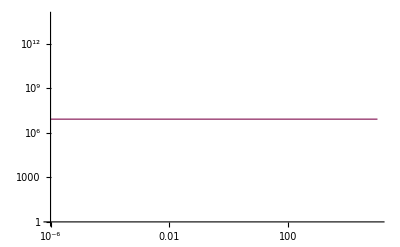

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

-Graphics-

```mathematica
ssac[κ_]:=Evaluate[(1/(solk[[4,1,2]]/.{ω->3.62}/.subnum))]
ssra[κ_]:=Evaluate[(1/(solk[[2,1,2]]/.{ω->3.62}/.subnum))]
LogLogPlot[{Re[ssac[t/a0]]/a0,Re[ssra[t/a0]]/a0},{t,0.000001,100000},PlotRange->{-1,1}]
LogLogPlot[{Re[ssac[t/a0]]/Im[ssac[t/a0]]/(2π),Re[ssra[t/a0]]/Im[ssra[t/a0]]/(2π)},{t,0.000001,100000},PlotRange->{-1,1}]
```

```mathematica
ssω0[kk_]:=NSolve[DIS2/.subnum/.{k->2π,κ->kk},ω]
```

```mathematica
drho=10^-4;
EQS1=EQS0/.subnum/.{k->2π}/.ssω0[kappa][[1]]/.{κ->kappa}/.{δρ->drho};
EQS2=EQS0/.subnum/.{k->2π}/.ssω0[kappa][[2]]/.{κ->kappa}/.{δρ->drho};
EQS3=EQS0/.subnum/.{k->2π}/.ssω0[kappa][[3]]/.{κ->kappa}/.{δρ->drho};
EQS4=EQS0/.subnum/.{k->2π}/.ssω0[kappa][[4]]/.{κ->kappa}/.{δρ->drho};
EQS5=EQS0/.subnum/.{k->2π}/.ssω0[kappa][[5]]/.{κ->kappa}/.{δρ->drho};
deltas=TableForm[{
Quiet[Join[{ω->ssω0[kappa][[1,1,2]]},{v[c]->ssω0[kappa][[1,1,2]]/(2π)},{"v[a]"->ssω0[kappa][[1,1,2]]/(2π)/a0},{δρ->drho},Quiet[Solve[Evaluate[EQS1],{δu,δu1,δEE,δF1}]][[1]]]],
Quiet[Join[{ω->ssω0[kappa][[2,1,2]]},{v[c]->ssω0[kappa][[2,1,2]]/(2π)},{"v[a]"->ssω0[kappa][[2,1,2]]/(2π)/a0},{δρ->drho},Quiet[Solve[Evaluate[EQS2],{δu,δu1,δEE,δF1}]][[1]]]],Quiet[Join[{ω->ssω0[kappa][[3,1,2]]},{v[c]->ssω0[kappa][[3,1,2]]/(2π)},{"v[a]"->ssω0[kappa][[3,1,2]]/(2π)/a0},{δρ->drho},Quiet[Solve[Evaluate[EQS3],{δu,δu1,δEE,δF1}]][[1]]]],Quiet[Join[{ω->ssω0[kappa][[4,1,2]]},{v[c]->ssω0[kappa][[4,1,2]]/(2π)},{"v[a]"->ssω0[kappa][[4,1,2]]/(2π)/a0},{δρ->drho},Quiet[Solve[Evaluate[EQS4],{δu,δu1,δEE,δF1}]][[1]]]],Quiet[Join[{ω->ssω0[kappa][[5,1,2]]},{v[c]->ssω0[kappa][[5,1,2]]/(2π)},{"v[a]"->ssω0[kappa][[5,1,2]]/(2π)/a0},{δρ->drho},Quiet[Solve[Evaluate[EQS5],{δu,δu1,δEE,δF1}]][[1]]]]
}]
```

Join[{ω→0.+0.01 ⅈ},{v[c]→0.+0.00159155 ⅈ},{v[a]→0.+0.159155 ⅈ},{δρ→1/10000},{}⟦1⟧]
Join[{ω→Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,1]},{v[c]→Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,1]/(2 π)},{v[a]→(50 Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,1])/π},{δρ→1/10000},{}⟦1⟧]
Join[{ω→Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,2]},{v[c]→Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,2]/(2 π)},{v[a]→(50 Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,2])/π},{δρ→1/10000},{}⟦1⟧]
Join[{ω→Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,3]},{v[c]→Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,3]/(2 π)},{v[a]→(50 Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,3])/π},{δρ→1/10000},{}⟦1⟧]
Join[{ω→Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,4]},{v[c]→Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,4]/(2 π)},{v[a]→(50 Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,4])/π},{δρ→1/10000},{}⟦1⟧]

```mathematica
nsol=4;
{N[out[[1,1]]] ,deltas[[1,nsol,4,2]]/out[[1,1]] } (* δρ/ρ *)
{0,deltas[[1,nsol,6,2]] } (* δu1/u1 *)
{N[out[[1,2]]] ,deltas[[1,nsol,5,2]]/out[[1,2]] } (* δu/u *)
{N[out[[1,8]]] ,deltas[[1,nsol,7,2]]/out[[1,8]]}(* δE/E *)
{N[out[[1,8]]] ,deltas[[1,nsol,8,2]]/out[[1,8]]}(* δF/E *)
{deltas[[1,nsol,1,2]]} (* ω *)
```

Part::partw: Part 2 of {δρ → 1/10000} does not exist.

{1.,Join[{ω→0.+0.01 ⅈ},{v[c]→0.+0.00159155 ⅈ},{v[a]→0.+0.159155 ⅈ},{δρ→1/10000},{}⟦1⟧]
Join[{ω→Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,1]},{v[c]→Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,1]/(2 π)},{v[a]→(50 Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,1])/π},{δρ→1/10000},{}⟦1⟧]
Join[{ω→Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,2]},{v[c]→Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,2]/(2 π)},{v[a]→(50 Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,2])/π},{δρ→1/10000},{}⟦1⟧]
Join[{ω→Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,3]},{v[c]→Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,3]/(2 π)},{v[a]→(50 Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,3])/π},{δρ→1/10000},{}⟦1⟧]
Join[{ω→Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,4]},{v[c]→Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,4]/(2 π)},{v[a]→(50 Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,4])/π},{δρ→1/10000},{}⟦1⟧]⟦1,4,4,2⟧}

Part::partw: Part 6 of Join[{ω → Root[(0.  - 1.49473×10^-107\ ⅈ)\ Bsq - (0.  + 5.60525×10^-108\ ⅈ)\ Power[« 2 »] + Plus[« 4 »]\ Slot[« 1 »] + Plus[« 6 »]\ Power[« 2 »] + Plus[« 6 »]\ Power[« 2 »] + Plus[« 6 »]\ Power[« 2 »] + Plus[« 6 »]\ Power[« 2 »] + Plus[« 4 »]\ Power[« 2 »] + Plus[« 4 »]\ Power[« 2 »] &, 3]}, {v[c] → Root[Times[« 2 »] + Times[« 2 »] + Times[« 2 »] + « 3 » + Times[« 2 »] + Times[« 2 »] + Times[« 2 »] &, 3]/2\ π}, {"v[a]" → 50\ Root[Times[« 2 »] + « 7 » + Times[« 2 »] &, 3]/π}, {δρ → 1/10000}, {} ⟦ 1 ⟧]
 does not exist.

{0,Join[{ω→0.+0.01 ⅈ},{v[c]→0.+0.00159155 ⅈ},{v[a]→0.+0.159155 ⅈ},{δρ→1/10000},{}⟦1⟧]
Join[{ω→Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,1]},{v[c]→Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,1]/(2 π)},{v[a]→(50 Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,1])/π},{δρ→1/10000},{}⟦1⟧]
Join[{ω→Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,2]},{v[c]→Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,2]/(2 π)},{v[a]→(50 Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,2])/π},{δρ→1/10000},{}⟦1⟧]
Join[{ω→Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,3]},{v[c]→Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,3]/(2 π)},{v[a]→(50 Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,3])/π},{δρ→1/10000},{}⟦1⟧]
Join[{ω→Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,4]},{v[c]→Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,4]/(2 π)},{v[a]→(50 Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,4])/π},{δρ→1/10000},{}⟦1⟧]⟦1,4,6,2⟧}

{0.0000900135,99985/9}

Part::partw: Part 7 of Join[{ω → Root[(0.  - 1.49473×10^-107\ ⅈ)\ Bsq - (0.  + 5.60525×10^-108\ ⅈ)\ Power[« 2 »] + Plus[« 4 »]\ Slot[« 1 »] + Plus[« 6 »]\ Power[« 2 »] + Plus[« 6 »]\ Power[« 2 »] + Plus[« 6 »]\ Power[« 2 »] + Plus[« 6 »]\ Power[« 2 »] + Plus[« 4 »]\ Power[« 2 »] + Plus[« 4 »]\ Power[« 2 »] &, 3]}, {v[c] → Root[Times[« 2 »] + Times[« 2 »] + Times[« 2 »] + « 3 » + Times[« 2 »] + Times[« 2 »] + Times[« 2 »] &, 3]/2\ π}, {"v[a]" → 50\ Root[Times[« 2 »] + « 7 » + Times[« 2 »] &, 3]/π}, {δρ → 1/10000}, {} ⟦ 1 ⟧]
 does not exist.

{6.0009×10^-7,1.66642×10^6 Join[{ω→0.+0.01 ⅈ},{v[c]→0.+0.00159155 ⅈ},{v[a]→0.+0.159155 ⅈ},{δρ→1/10000},{}⟦1⟧]
Join[{ω→Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,1]},{v[c]→Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,1]/(2 π)},{v[a]→(50 Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,1])/π},{δρ→1/10000},{}⟦1⟧]
Join[{ω→Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,2]},{v[c]→Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,2]/(2 π)},{v[a]→(50 Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,2])/π},{δρ→1/10000},{}⟦1⟧]
Join[{ω→Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,3]},{v[c]→Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,3]/(2 π)},{v[a]→(50 Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,3])/π},{δρ→1/10000},{}⟦1⟧]
Join[{ω→Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,4]},{v[c]→Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,4]/(2 π)},{v[a]→(50 Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,4])/π},{δρ→1/10000},{}⟦1⟧]⟦1,4,7,2⟧}

Part::partw: Part 8 of Join[{ω → Root[(0.  - 1.49473×10^-107\ ⅈ)\ Bsq - (0.  + 5.60525×10^-108\ ⅈ)\ Power[« 2 »] + Plus[« 4 »]\ Slot[« 1 »] + Plus[« 6 »]\ Power[« 2 »] + Plus[« 6 »]\ Power[« 2 »] + Plus[« 6 »]\ Power[« 2 »] + Plus[« 6 »]\ Power[« 2 »] + Plus[« 4 »]\ Power[« 2 »] + Plus[« 4 »]\ Power[« 2 »] &, 3]}, {v[c] → Root[Times[« 2 »] + Times[« 2 »] + Times[« 2 »] + « 3 » + Times[« 2 »] + Times[« 2 »] + Times[« 2 »] &, 3]/2\ π}, {"v[a]" → 50\ Root[Times[« 2 »] + « 7 » + Times[« 2 »] &, 3]/π}, {δρ → 1/10000}, {} ⟦ 1 ⟧]
 does not exist.

{6.0009×10^-7,1.66642×10^6 Join[{ω→0.+0.01 ⅈ},{v[c]→0.+0.00159155 ⅈ},{v[a]→0.+0.159155 ⅈ},{δρ→1/10000},{}⟦1⟧]
Join[{ω→Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,1]},{v[c]→Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,1]/(2 π)},{v[a]→(50 Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,1])/π},{δρ→1/10000},{}⟦1⟧]
Join[{ω→Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,2]},{v[c]→Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,2]/(2 π)},{v[a]→(50 Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,2])/π},{δρ→1/10000},{}⟦1⟧]
Join[{ω→Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,3]},{v[c]→Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,3]/(2 π)},{v[a]→(50 Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,3])/π},{δρ→1/10000},{}⟦1⟧]
Join[{ω→Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,4]},{v[c]→Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,4]/(2 π)},{v[a]→(50 Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,4])/π},{δρ→1/10000},{}⟦1⟧]⟦1,4,8,2⟧}

Part::partw: Part 2 of {ω → Root[(0.  - 1.49473×10^-107\ ⅈ)\ Bsq - (0.  + 5.60525×10^-108\ ⅈ)\ Bsq^3/2 + (Times[« 2 »] + Times[« 2 »] + Times[« 2 »] + Times[« 2 »])\ #1 + « 3 » + ((-2.39874×10^-102 + 0.\ ⅈ) + Times[« 2 »] + Times[« 2 »] + Times[« 2 »] + Times[« 2 »] + Times[« 2 »])\ Slot[« 1 »]^5 + ((0.  - 3.69312×10^-105\ ⅈ) + Times[« 2 »] + Times[« 2 »] + Times[« 2 »])\ Slot[« 1 »]^6 + ((1.82226×10^-103 + 0.\ ⅈ) + Times[« 2 »] + Times[« 2 »] + Times[« 2 »])\ Slot[« 1 »]^7 &, 3]}
 does not exist.

{Join[{ω→0.+0.01 ⅈ},{v[c]→0.+0.00159155 ⅈ},{v[a]→0.+0.159155 ⅈ},{δρ→1/10000},{}⟦1⟧]
Join[{ω→Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,1]},{v[c]→Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,1]/(2 π)},{v[a]→(50 Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,1])/π},{δρ→1/10000},{}⟦1⟧]
Join[{ω→Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,2]},{v[c]→Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,2]/(2 π)},{v[a]→(50 Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,2])/π},{δρ→1/10000},{}⟦1⟧]
Join[{ω→Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,3]},{v[c]→Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,3]/(2 π)},{v[a]→(50 Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,3])/π},{δρ→1/10000},{}⟦1⟧]
Join[{ω→Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,4]},{v[c]→Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,4]/(2 π)},{v[a]→(50 Root[(0.-1.49473×10^-107 ⅈ) Bsq-(0.+5.60525×10^-108 ⅈ) Bsq^(3/2)+((9.34216×10^-104+0. ⅈ) Bsq+(3.50331×10^-104+0. ⅈ) Bsq^(3/2)+6.22717×10^-100 Bsq^2+2.33519×10^-100 Bsq^(5/2)) #1+((0.-1.51471×10^-108 ⅈ)-(0.+9.45457×10^-125 ⅈ) √Bsq+(0.+6.45327×10^-105 ⅈ) Bsq+(0.+5.34802×10^-107 ⅈ) Bsq^(3/2)+(0.+9.46409×10^-103 ⅈ) Bsq^2+(0.+3.54904×10^-103 ⅈ) Bsq^(5/2)) #1^2+((9.46701×10^-105+0. ⅈ)+(1.4388×10^-112+0. ⅈ) √Bsq+(5.52112×10^-101+0. ⅈ) Bsq+(3.54942×10^-101+0. ⅈ) Bsq^(3/2)-(3.15469×10^-101+0. ⅈ) Bsq^2-(1.18301×10^-101+0. ⅈ) Bsq^(5/2)) #1^3+((0.+6.5399×10^-106 ⅈ)-(0.+4.796×10^-111 ⅈ) √Bsq+(0.+8.37613×10^-104 ⅈ) Bsq+(0.+5.39483×10^-104 ⅈ) Bsq^(3/2)+(0.+2.39728×10^-104 ⅈ) Bsq^2+(0.+8.98981×10^-105 ⅈ) Bsq^(5/2)) #1^4+((-2.39874×10^-102+0. ⅈ)+(5.99505×10^-103+0. ⅈ) √Bsq-(5.39488×10^-102+0. ⅈ) Bsq-(2.39771×10^-102+0. ⅈ) Bsq^(3/2)-(1.19864×10^-102+0. ⅈ) Bsq^2-(4.49491×10^-103+0. ⅈ) Bsq^(5/2)) #1^5+((0.-3.69312×10^-105 ⅈ)+(0.+9.11132×10^-106 ⅈ) √Bsq-(0.+1.84628×10^-105 ⅈ) Bsq+(0.+4.55498×10^-106 ⅈ) Bsq^(3/2)) #1^6+((1.82226×10^-103+0. ⅈ)-(4.55566×10^-104+0. ⅈ) √Bsq+(9.10995×10^-104+0. ⅈ) Bsq-(2.27749×10^-104+0. ⅈ) Bsq^(3/2)) #1^7&,4])/π},{δρ→1/10000},{}⟦1⟧]⟦1,4,1,2⟧}

```mathematica
7
```

7